```mathematica
ClearAll["Global`*"]
```

```mathematica
L=2;
h=1;
```

```mathematica
fexact[x_]:=Cos[2 π x]/(1+10 x)
```

```mathematica
vexact[x_,y_]:={Cos[2 π x]/(1+10 x),Sin[2π x]/(1+3 x^2)}
```

```mathematica
texact[x_,y_]:={{Cos[2 π x ]/(1+10 x),Sin[2 π x]/(1+3 x^2)},{Cos[9 π x]/(1+3 x^2),Sin[12 π x^2]/(1+3x^2)}}
```

```mathematica
f = Import ["/Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u/two_domains/solution/f_mesh.csv"]
```

```mathematica
v= Import ["/Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u/two_domains/solution/v_mesh.csv"]
```

```mathematica
t = Import ["/Users/michelecastellana/Desktop/t_mesh.csv"]
```

```mathematica
(*read scalar field*)
```

```mathematica
ϵ=1*^-3;
For[tf={};i=1,i<=Length[f],i++,
If[Abs[f[[i,3]]-h]<ϵ,AppendTo[tf,{f[[i,2]],f[[i,1]]}]]
]
```

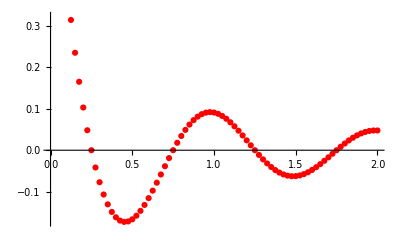

```mathematica
Show[ListPlot[tf,PlotStyle->Red],Plot[fexact[x,h],{x,0,L}]]
```

```mathematica
(*read tensor field*)
```

```mathematica
ϵ=1*^-3;
For[tt={};i=1,i<=Length[t],i++,
If[Abs[t[[i,11]]-h]<ϵ,AppendTo[tt,{t[[i,10]],Table[t[[i,j]],{j,1,9}]}]]
]
```

```mathematica
tt
```

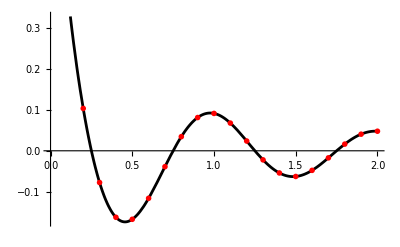

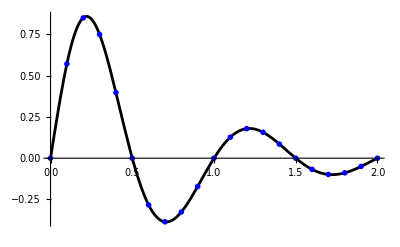

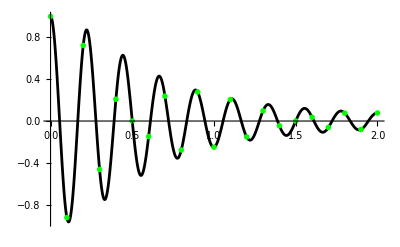

```mathematica
Show[Plot[texact[x,h][[1,1]],{x,0,L},PlotStyle->Black],ListPlot[Table[{tt[[i,1]],tt[[i,2,1]]},{i,1,Length[tt]}],PlotStyle->{Red,PointSize->0.01}]]
Show[Plot[texact[x,h][[1,2]],{x,0,L},PlotStyle->Black],ListPlot[Table[{tt[[i,1]],tt[[i,2,2]]},{i,1,Length[tt]}],PlotStyle->{Blue,PointSize->0.01}]]
Show[Plot[texact[x,h][[2,1]],{x,0,L},PlotStyle->Black],ListPlot[Table[{tt[[i,1]],tt[[i,2,4]]},{i,1,Length[tt]}],PlotStyle->{Green,PointSize->0.01}]]
```